```mathematica
ClearAll["Global`*"]
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
data = Import[NotebookDirectory[]<>"SpherePlaneResistance.txt","Table"];
ξdata=data[[All,1]];
XAdata=data[[All,2]];
YAdata=data[[All,3]];
YBdata=data[[All,4]];
XCdata=data[[All,5]];
YCdata=data[[All,6]];
δ=0.01;
YAVal=Interpolation[Transpose[{ξdata,YAdata}]][δ];
YBVal=Interpolation[Transpose[{ξdata,YBdata}]][δ];
YCVal=Interpolation[Transpose[{ξdata,YCdata}]][δ];
XAVal=Interpolation[Transpose[{ξdata,XAdata}]][δ];
XCVal=Interpolation[Transpose[{ξdata,XCdata}]][δ];
AA={{YAVal,0,0},{0,YAVal,0},{0,0,XAVal}};
BB={{0,YBVal,0},{-YBVal,0,0},{0,0,0}};
CC={{YCVal,0,0},{0,YCVal,0},{0,0,XCVal}};
Resistance=ArrayFlatten[ {{AA,Transpose[BB]},{BB,CC}}];
```

```mathematica
listω1=Table[i,{i,0.1,0.4,0.1}]
```

{0.1,0.2,0.3,0.4}

```mathematica
listVr={};
listV={};
list={};
For[j=1,j<61,j++,
ω1=0.3;
ω2=0.01;
ω3=-0.002;
angle=j;
parameter={ω1,ω2,ω3,angle};
anitropy=0.01;
tMax = 200 2 π/parameter[[1]];
(*first field is magnetic , second is gravity*)
field={True,False};
B[{ω1_,ω2_,ω3_,angle_},t_]:={  Sin[  ω1 t] Sin[  ω2   t] ,Sin[  ω1 t] Cos[  ω2 t]  ,Cos[ ω1 t ]   }.RotationMatrix[angle Degree*Boole[field[[1]]] ,{0,1,0}];
Rq={{q0^2+q1^2-q2^2-q3^2,2q1 q2+2q0 q3,2q1 q3-2q0 q2},
{2q1 q2-2q0 q3,q0^2-q1^2+q2^2-q3^2,2q2 q3+2q0 q1},
{2 q1 q3+2 q0 q2,2q2 q3-2 q0 q1, q0^2-q1^2-q2^2+q3^2}};
(*magnetic moment*)
mq=Simplify[Transpose[Rq] .{0,0,1}   ];
Lq=Simplify[Cross[mq,B[parameter,t ]]];
(*force *)
F ={Sin[parameter[[4]] Degree] *anitropy*Boole[field[[2]]] ,0,0};
FLq=ArrayFlatten[{F,Lq},1];
UΩq=Simplify[Inverse[Resistance].FLq];
Uq=UΩq[[1;;3]];
Ωq=UΩq[[4;;6]];
Q ={{q0 ,-q1,-q2,-q3},
{q1,q0,q3,-q2},
{q2,-q3,q0,q1},
{q3,q2,-q1,q0}};
(*equation 156*)
quaternionRate=1/2 Q.ArrayFlatten[{{0},Ωq},1];
q={Cos[ϕ/2]Cos[θ/2]Cos[ψ/2]-Sin[ϕ/2]Cos[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Sin[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2],
Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]+Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]};
qIC = q/.{ϕ->RandomReal[2 π]*0,θ->RandomReal[2 π]*0,ψ->RandomReal[2 π]*0};
para={q0->q0[t],q1->q1[t],q2->q2[t],q3->q3[t]};
sol=NDSolve[{
q0'[t]==(quaternionRate[[1]]/.para),
q1'[t]==(quaternionRate[[2]]/.para),
q2'[t]==(quaternionRate[[3]]/.para),
q3'[t]==(quaternionRate[[4]]/.para),
x'[t]==(Uq[[1]]/.para),
y'[t]==(Uq[[2]]/.para),
q0[0]==qIC[[1]],
q1[0]==qIC[[2]],
q2[0]==qIC[[3]],
q3[0]==qIC[[4]],
x[0]==0,
y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},{t,0,tMax}];
data=Table[x[t]/.sol[[1]],{t,0,tMax,0.2}];
peaks=FindPeaks[data,50,0,1];
(*data2=Table[y[t]/.sol[[1]],{t,0,tMax}];

peaksy=FindPeaks[data2,30,0,1];
miny=FindPeaks[-data2,30,0,1];
r=miny[[1,2]]+peaksy[[1,2]];
vr={ω1,ω2,Differences[peaks][[1,2]]/r};*)
v={angle,Differences[peaks][[1,2]]/Differences[peaks][[1,1]]};
(*listVr=Append[listVr,vr];
listV=Append[listV,v];*)
list=Append[list,v];
]


(*ParametricPlot[{x[t]/.sol[[1]],y[t]/.sol[[1]]},{t,0,tMax},PlotRange->{{-10,10},{-10,10}},PlotStyle->{Red, Thick},Frame->True]*)
```

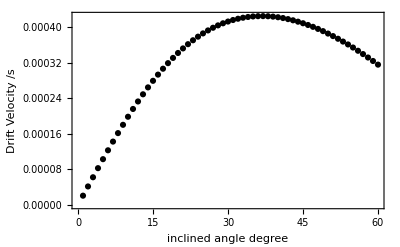

```mathematica
ListPlot[
list
,PlotRange->All,PlotStyle->{{Black}},Frame->True,FrameLabel->{"inclined  angle degree","Drift Velocity /s"},LabelStyle->Directive[Black,Bold],
FrameTicksStyle->Directive[Black,12]

]
```

```mathematica
ListPlot[{

Table[{i+9,listVr[[1;;91]][[i,3]]},{i,1,91}],
Table[{i+9,listVr[[91;;91+90]][[i,3]]},{i,1,91}],
Table[{i+9,listVr[[91+90+1;;91+90+1+90]][[i,3]]},{i,1,91}]

}

,PlotRange->All,PlotStyle->{{Black},{Red},{Blue}},Frame->True,FrameLabel->{"ω1/ω2","Drift Velocity /r"},LabelStyle->Directive[Black,Bold],
FrameTicksStyle->Directive[Black,12]
,PlotLegends->{"ω1=0.1","ω2=0.2","ω3=0.3"}
]
```

```mathematica
Export["listV.csv",listV]
```

listV.csv

```mathematica
Export["listVr.csv",listVr]
```

listVr.csv

{{-1,-1,-1,-1,-1},{-1,-1,-1,-1,1},{-1,-1,-1,1,-1},{-1,-1,-1,1,1},{-1,-1,1,-1,-1},{-1,-1,1,-1,1},{-1,-1,1,1,-1},{-1,-1,1,1,1},{-1,1,-1,-1,-1},{-1,1,-1,-1,1},{-1,1,-1,1,-1},{-1,1,-1,1,1},{-1,1,1,-1,-1},{-1,1,1,-1,1},{-1,1,1,1,-1},{-1,1,1,1,1},{1,-1,-1,-1,-1},{1,-1,-1,-1,1},{1,-1,-1,1,-1},{1,-1,-1,1,1},{1,-1,1,-1,-1},{1,-1,1,-1,1},{1,-1,1,1,-1},{1,-1,1,1,1},{1,1,-1,-1,-1},{1,1,-1,-1,1},{1,1,-1,1,-1},{1,1,-1,1,1},{1,1,1,-1,-1},{1,1,1,-1,1},{1,1,1,1,-1},{1,1,1,1,1}}

```mathematica
sign
```

{-1,-1,-1,-1,-1}

```mathematica
sign=Tuples[{-1,1},5][[32]];
ω1=0.2;
ω2=0.01;
ω3=-0.002;
angle=10.0;
parameter={ω1,ω2,ω3,angle};
anitropy=0.01;
tMax = 200 2 π/parameter[[1]];
(*first field is magnetic , second is gravity*)
field={True,False};

B[{ω1_,ω2_,ω3_,angle_},t_]:={  Sin[ sign[[1]] ω1 t] Sin[sign[[2]] ω2   t] ,Sin[ sign[[3]] ω1 t] Cos[sign[[4]]  ω2 t]  ,Cos[sign[[5]]ω1 t ]   }.RotationMatrix[angle Degree*Boole[field[[1]]] ,{0,1,0}];
Rq={{q0^2+q1^2-q2^2-q3^2,2q1 q2+2q0 q3,2q1 q3-2q0 q2},
{2q1 q2-2q0 q3,q0^2-q1^2+q2^2-q3^2,2q2 q3+2q0 q1},
{2 q1 q3+2 q0 q2,2q2 q3-2 q0 q1, q0^2-q1^2-q2^2+q3^2}};
(*magnetic moment*)
mq=Simplify[Transpose[Rq] .{0,0,1}   ];
Lq=Simplify[Cross[mq,B[parameter,t ]]];
(*force *)
F ={Sin[parameter[[4]] Degree] *anitropy*Boole[field[[2]]] ,0,0};
FLq=ArrayFlatten[{F,Lq},1];
UΩq=Simplify[Inverse[Resistance].FLq];
Uq=UΩq[[1;;3]];
Ωq=UΩq[[4;;6]];
Q ={{q0 ,-q1,-q2,-q3},
{q1,q0,q3,-q2},
{q2,-q3,q0,q1},
{q3,q2,-q1,q0}};
(*equation 156*)
quaternionRate=1/2 Q.ArrayFlatten[{{0},Ωq},1];
q={Cos[ϕ/2]Cos[θ/2]Cos[ψ/2]-Sin[ϕ/2]Cos[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Sin[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2],
Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]+Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]};
qIC = q/.{ϕ->RandomReal[2 π]*0,θ->RandomReal[2 π]*0,ψ->RandomReal[2 π]*0};
para={q0->q0[t],q1->q1[t],q2->q2[t],q3->q3[t]};
sol=NDSolve[{
q0'[t]==(quaternionRate[[1]]/.para),
q1'[t]==(quaternionRate[[2]]/.para),
q2'[t]==(quaternionRate[[3]]/.para),
q3'[t]==(quaternionRate[[4]]/.para),
x'[t]==(Uq[[1]]/.para),
y'[t]==(Uq[[2]]/.para),
q0[0]==qIC[[1]],
q1[0]==qIC[[2]],
q2[0]==qIC[[3]],
q3[0]==qIC[[4]],
x[0]==0,
y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},{t,0,tMax}];
```

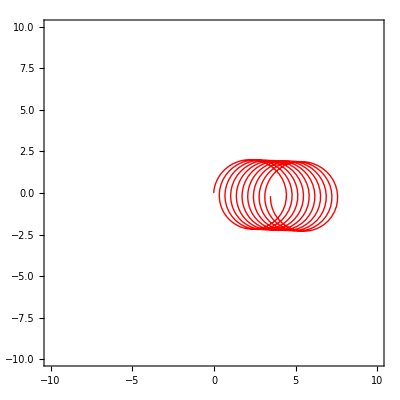

```mathematica
ParametricPlot[{x[t]/.sol[[1]],y[t]/.sol[[1]]},{t,0,tMax},PlotRange->{{-10,10},{-10,10}},PlotStyle->{Red, Thick},Frame->True,Axes->False]
```

```mathematica
ParametricPlot3D[B[parameter,t],{t,0,tMax},PlotStyle->{Black},PlotRange->{All,All,All},
AxesLabel->{Style[x,Large,Bold,MPLColorMap["Plasma"][0.3]],Style[y,Large,Bold,MPLColorMap["Plasma"][0.6]],Style[z,Large,Bold,MPLColorMap["Plasma"][0.9]]}]
```

-Graphics3D-

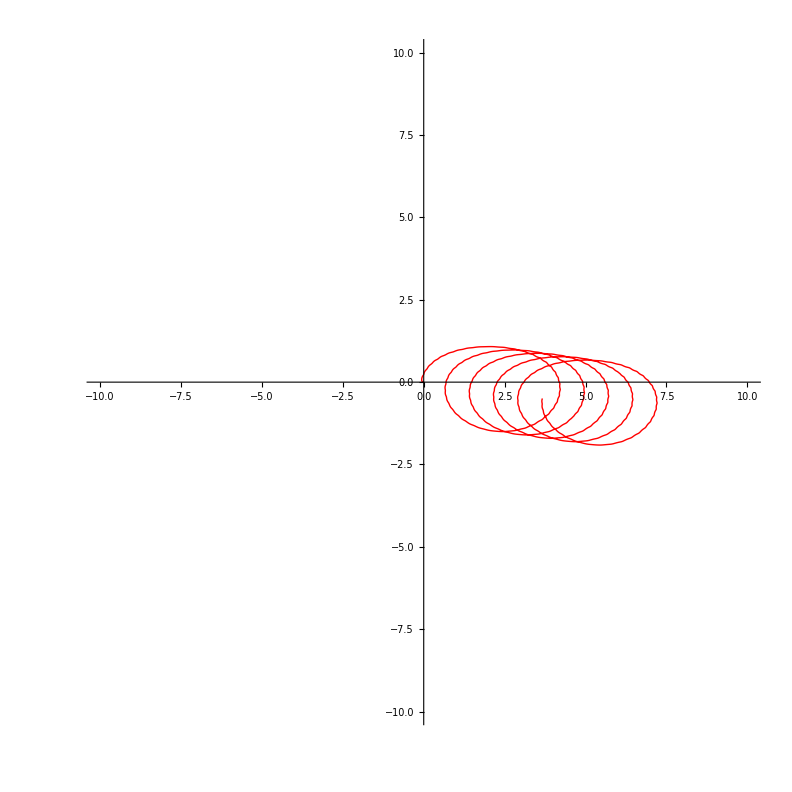

```mathematica
Manipulate[
Show[
Graphics3D[{Opacity[0.2],Sphere[{0,0,0},1]},PlotRange->{{-1,1},{-1,1},{-1,1}}],
Graphics3D[{Red,AbsoluteThickness[2],Arrow[{{0,0,0}, B[parameter,t] }]}]

]
,{t,1,30}]
```